# N-photon emission from an organic single molecule

Vladislav Bushmakin, Ilja Gerhardt

PI 3 Uni Stuttgart

Abstract

The coherent control over the population of  quantum emitters excited state is a promising tool for single photon sources engineering. Beyond the generation of single photons a quantum emitter can preferably emit two photons, if driven by a 2π  pulse. Here we study the factors defining the probability of such two-photon pulses generation, such as the coherence properties of the emitter and the driving pulse intensity and length. In addition, we explore the difference between the Rabi rotations and the Rabi oscillations of a two-level system’s excited state population.

31.01.2021

## Introduction

The optical quantum technologies strongly rely on the ability to generate non-classical states of light. On the most promising approaches is the use of single quantum emitters as a source of single photons. A quantum emitter can be approximated as a two-level system, hence when driven by a short laser pulse resonant to the transition it’s excited state population can be deterministically controlled. The inversion with a laser pulse of a two-level system population opens a way to deterministic generation of single photons. Moreover, if a system is driven with a 2π pulse instead of a π pulse the resulting emission preferablly consists of two-photons.

A two-level system driven by a continuous laser field

Solving the Lindblad equations describing the dynamics of the density matrix of a two-level system driven by a laser field \cite{1.} we can obtain the expression for the probability to find a system in the excited state only once:

```mathematica
-Graphics-;
```

In other words, to estimate the probability a N-th emission occurred we assume the spontaneous decay undergoes the transition to an effective “buffer” state equivalent to the ground state |g1>, but artificially off-resonant to the driving field. The decay rate from the excited state to this artificial ground state |g2>  is assumed to be Γ1. The off-diagonal elements of the density matrix are coupled via the driving field with coupling straingth Ω Rabi and via the “pure” dephasing term γϕ.  The resulting expression yields:

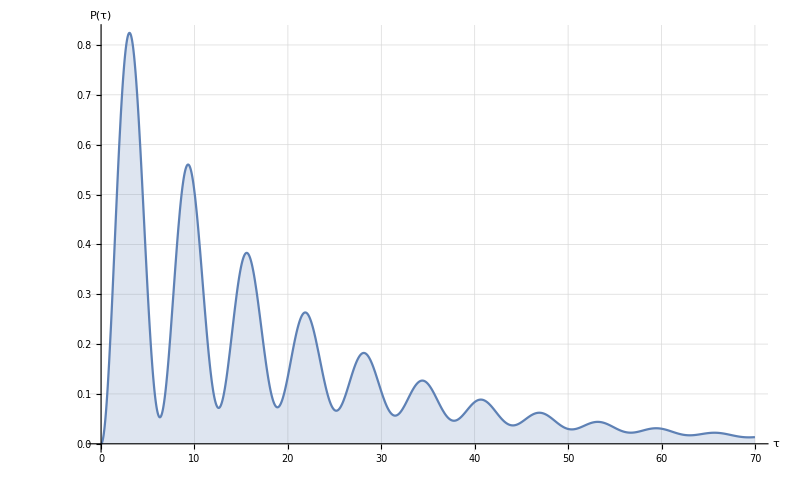

```mathematica
ns = 10^-9;
MHz = 10^6;
Subscript[γ, 10] = 0;
Γ0 =  0;
η = 0;
Γ = 1/2(Γ1 + Subscript[γ, ϕ]);
P[τ_] :=  1/2*(Exp[- 1/2 Γ1 * τ]+ Exp[-1/4(2Γ + Γ1 ) * τ]*Sin[Ω*τ + Θ]);


varParams = {Θ -> -1.6, Ω -> 1000 MHz, Γ1 -> 1/(10 ns), Subscript[γ, ϕ] -> 1/(10 ns)};
plt1 = Plot[{{P[τ ns] /. varParams}}, {τ,0,70}, PlotRange-> All,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0,LabelStyle->(FontSize->25), PlotStyle -> Automatic, AxesLabel->{"τ", "P(τ)"}]
```

```mathematica
Pnorm1 = Integrate[P[τ],{τ, 0, ∞}];
P2a =Integrate[P[t]*P[τ - t], {t, 0, τ}];
Pnorm2 = Pnorm1^2;
P2at[τ_] =P2a;
P3a =Integrate[P2at[t]*P[τ - t], {t, 0, τ}];
Pnorm3 = Pnorm1^3;
P3at[τ_] =P3a;
```

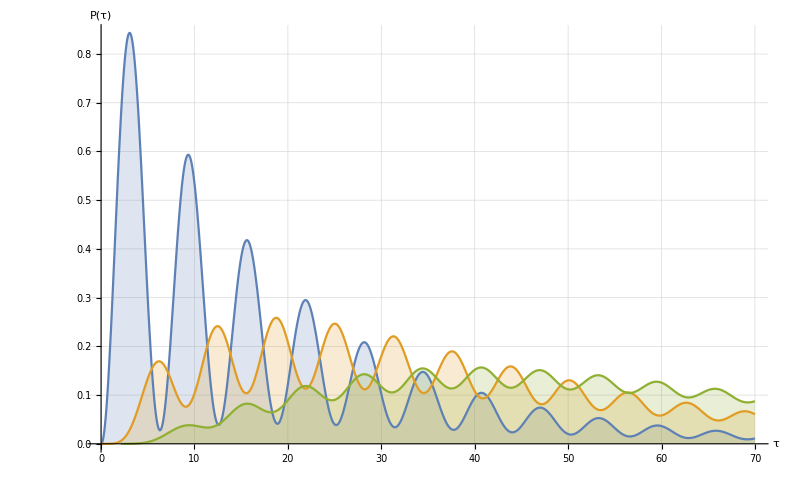

```mathematica
varParams = {Θ -> -1.6, Ω -> 1000 MHz, Γ1 -> 1/(10 ns), Subscript[γ, ϕ] -> 1/(20 ns)};
plt1 = Plot[{{P[τ*ns]/(10^8 Pnorm1) /. varParams},{P2at[τ*ns]/(10^8 Pnorm1^2)/. varParams},{P3at[τ*ns]/(10^8 Pnorm1^3) /. varParams}}, {τ,0,70}, PlotRange-> All,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0,LabelStyle->(FontSize->25), PlotStyle -> Automatic, AxesLabel->{"τ", "P(τ)"}]
```

The given plot demonstrates the probability P to detect one (blue), two (orange) or three (green) photons at time τ, if the system is driven continuously.

A two-level system driven by a laser pulse

```mathematica
P1p[τ_]:= P[τ] * (HeavisideTheta[pulselen - τ/ns]) + (HeavisideTheta[-pulselen + τ/ns]) * A * Exp[-a * (τ - pulselen ns)] * P[pulselen ns];
P2p[τ_]:= P2at[τ] * (HeavisideTheta[pulselen - τ/ns]) + (HeavisideTheta[-pulselen + τ/ns]) * A * Exp[-a * (τ - pulselen ns)] * P2at[pulselen ns];
P3p[τ_]:= P3at[τ] * (HeavisideTheta[pulselen - τ/ns]) + (HeavisideTheta[-pulselen + τ/ns]) * A * Exp[-a * (τ - pulselen ns)] * P3at[pulselen ns];
```

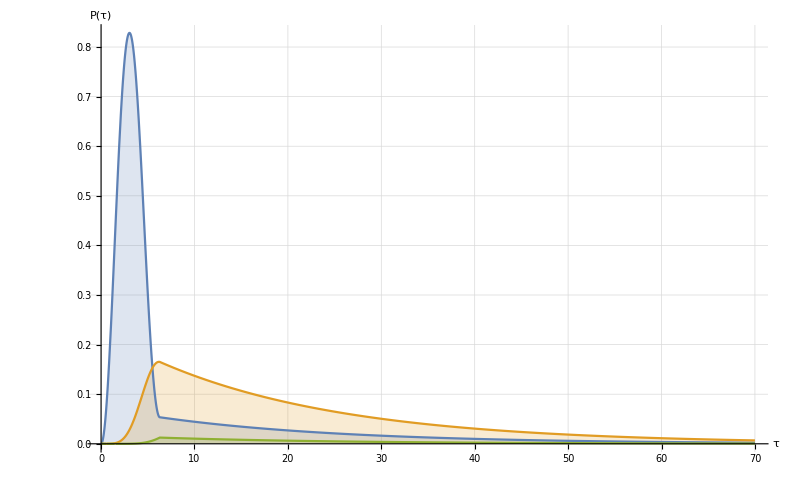

```mathematica
Ω0 = 1000 MHz;
pulseLength = (2π)/(Ω0 ns);
varParams = {Θ -> -1.6, Ω -> Ω0, Γ1 -> 1/(10 ns), Subscript[γ, ϕ] -> 1/(10 ns),pulselen ->  pulseLength};
plt1 = Plot[{{P1p[τ*ns]/(10^8 Pnorm1) /. varParams},{P2p[τ*ns]/(10^8 Pnorm1^2)/. varParams},{P3p[τ*ns]/(10^8 Pnorm1^3) /. varParams}}, {τ,0,70}, PlotRange-> All,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0,LabelStyle->(FontSize->25), PlotStyle -> Automatic, AxesLabel->{"τ", "P(τ)"}]
```

The given plot demonstrates the probability P to detect one (blue), two (orange) or three (green) photons at time τ, if the system is driven by a pulse with length pulselen.

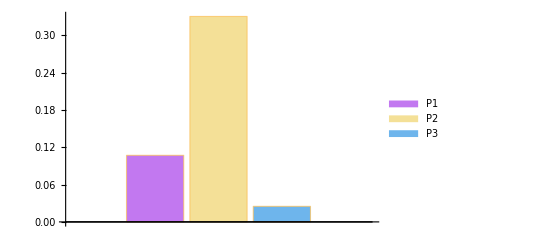

```mathematica
BarChart[{(P1p[pulseLength ns]/(10^8 Pnorm1)/. varParams)/HeavisideTheta[0],(P2p[pulseLength ns]/(10^8 Pnorm1^2)/. varParams)/HeavisideTheta[0], Re[(P3p[pulseLength ns]/(10^8 Pnorm1^3)/. varParams)/HeavisideTheta[0]]}, ChartLegends->{"P1", "P2", "P3"}, ChartStyle->"Pastel"]
```

The given bar chart demonstrates the probability P to detect first (blue), second (orange) or third (green) photon emitted by a two-level system after the excitation pulse with length pulselen.

Secod-order correlation function

As the emission proceeds consecutively the value of the second order correlation function will substantially depend on the binning.

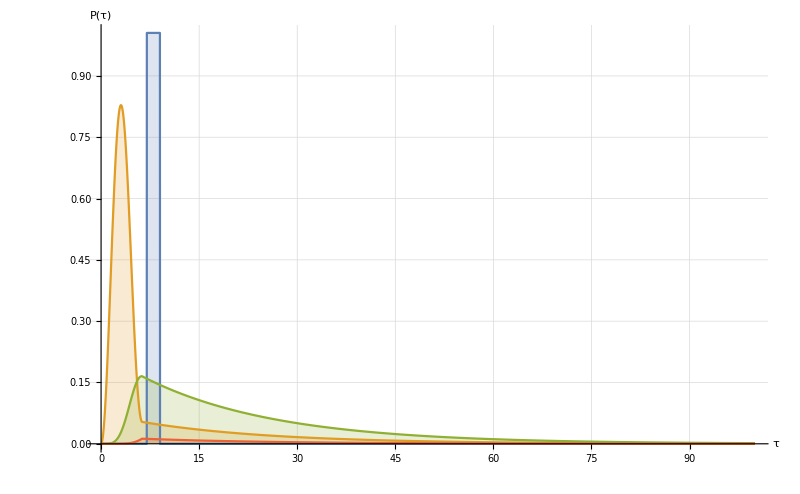

```mathematica
binWidth = 1;
pltM = Plot[{{UnitStep[binWidth - (τ - 8)^2]/Pnorm1 /. varParams}/10^8,{P1p[τ ns]/(10^8 Pnorm1) /. varParams}, {P2p[τ ns]/(10^8 Pnorm2)/. varParams}, {P3p[τ ns]/(10^8 Pnorm3)/. varParams}}, {τ,0,100},PlotRange-> All,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0,LabelStyle->(FontSize->25), PlotStyle -> Automatic, AxesLabel->{"τ", "P(τ)"}]
```

```mathematica
binWidth = 0.1;

Pbin1 = Table[NIntegrate[P1p[t ns]/(Pnorm1*10^8)*UnitStep[binWidth - (τ - t)^2] /. varParams, {t, 0, 20}], {τ, 0, 20, binWidth/2}];
Pbin2 = Table[NIntegrate[P2p[t ns]/(Pnorm2 * 10^8)*UnitStep[binWidth - (τ - t)^2] /. varParams, {t, 0, 20}], {τ, 0, 20, binWidth/2}];
Pbin3 = Table[ NIntegrate[P3p[t ns]/(Pnorm3 * 10^8)*UnitStep[binWidth - (τ - t)^2] /. varParams, {t, 0, 20}], {τ, 0, 20, binWidth/2}];
```

```mathematica
ListPlot[ (2*(Pbin2) + 6*(Pbin3))/(Pbin1 + 2*(Pbin2) + 3*(Pbin3))^2 /.varParams, GridLines -> Automatic, ImageSize-> 800, LabelStyle ->(FontSize->25), PlotStyle -> Automatic, AxesLabel->{"τ", "g^(2)(0)"}]
```

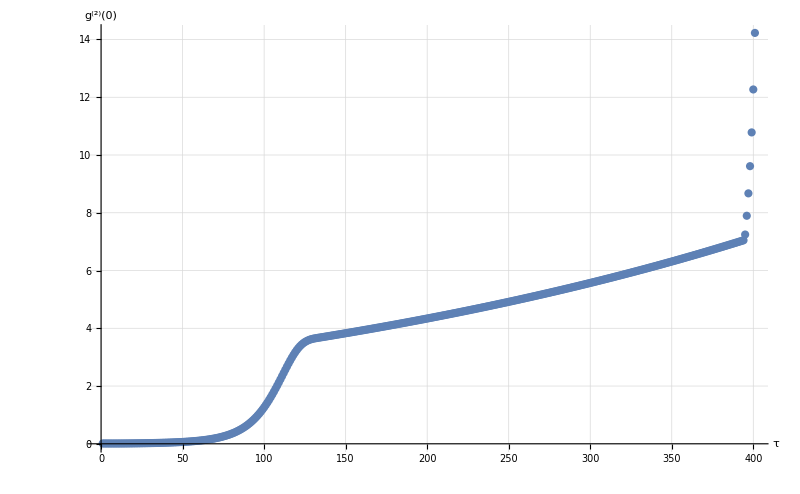

```mathematica
(2*(Total[Pbin2]) + 6*(Total[Pbin3]))/(Total[Pbin1] + 2*(Total[Pbin2]) + 3*(Total[Pbin3]))^2 * (Total[Pbin1] + Total[Pbin2] + Total[Pbin3])
```

0.443226

```mathematica
Total[Pbin1]
```

40.7232

1. Kosugi, N., Matsuo, S., Konno, K. & Hatakenaka, N. Theory of damped Rabi oscillations. Phys. Rev. B - Condens. Matter Mater. Phys. 72, 2–5 (2005).

2. Fischer, Kevin A., et al. “Signatures of two-photon pulses from a quantum two-level system.” Nature Physics 13.7 (2017).

3. Muñoz, C. Sánchez, et al. “Emitters of N-photon bundles.” Nature photonics 8.7 (2014)

4. Stevens, Martin J., et al. “Third-order antibunching from an imperfect single-photon source.” Quantum Electronics and Laser Science Conference. Optical Society of America, 2011

5. Loredo, J. C., et al. “Generation of non-classical light in a photon-number superposition.” Nature Photonics 13.11 (2019)